```mathematica
loadNotebook["uproszczony_off_7_model.nb"];

wyliczSterowanie[wd_,w_,k1_]:=(
M= Inverse[D[w,{qu[t]}].G2u ];
Det[D[w,{qu[t]}].G2u ] // Simplify // Print;
K1=k1*IdentityMatrix[3];
M=M.(D[wd,t]-K1.(w-wd));
M = M /.{l-> 0.1, R-> 0.03, Subscript[r, 1]->0.02, Subscript[r, 2]->0.02};
M
);

rozwiazRownania[M_,q0_,tmax_]:=(
pstrona = Transpose[G2u.Transpose[{ηu[t]}]][[1]];
lstrona = D[qu[t],t];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.{Subscript[η, 1][t] ->M[[1]], Subscript[η, 2][t]->M[[2]],Subscript[η, 3][t]->M[[3]],l-> 0.1, Subscript[r, 1]->0.02, Subscript[r, 2]->0.02}) ~Join~  q0;
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],Subscript[θ, u1], Subscript[ϕ, u1],Subscript[θ, u2], Subscript[ϕ, u2]}, {t,0,tmax}, Method->Automatic, MaxSteps->1000000];
roz
);
wyrysuj[rozwiazanieu_, w_,wd_,tmax_,anim_]:=Module[{},
Plot[w[[1]]-wd[[1]]/.rozwiazanieu,{t,0,tmax}, PlotRange->All, AxesLabel->{"t","ex"}] //Print;
Plot[w[[2]]-wd[[2]]/.rozwiazanieu,{t,0,tmax}, PlotRange->All, AxesLabel->{"t","ey"}] //Print;
Plot[Evaluate[{Subscript[θ, u1][t],  Subscript[θ, u2][t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","skrecenie"}, PlotStyle->{Red, Blue}, PlotLegends->{"θ_u1",  "θ_u2"}] //Print;
Plot[Evaluate[{Subscript[ϕ, u1]'[t],  Subscript[ϕ, u2]'[t]} /.rozwiazanieu], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","predkosc"},PlotStyle->{Red, Blue}, PlotLegends->{"ϕ_u1",  "ϕ_u2"}] //Print;

krzywa1u[t_] = {x[t] ,y[t]} /. rozwiazanieu;

xu[t_] = (x[t]/.rozwiazanieu)[[1]]  ;
yu[t_] = (y[t]/.rozwiazanieu)[[1]]  ;

x1u[t_] = ((x[t]+l*Sin[Subscript[θ, 0][t]]) /. rozwiazanieu  /. {l-> 0.1, R-> 0.03})[[1]];
y1u[t_] = ((y[t]-l*Cos[Subscript[θ, 0][t]]) /. rozwiazanieu  /. {l-> 0.1, R-> 0.03})[[1]];
krzywasu[t_] = ({x1u[t], y1u[t]} /. rozwiazanieu);

x2u[t_] = ((x[t]+2l*Sin[Subscript[θ, 0][t]]) /. rozwiazanieu /. {l-> 0.1, R-> 0.03})[[1]];
y2u[t_] = ((y[t]-2l*Cos[Subscript[θ, 0][t]]) /. rozwiazanieu /. {l-> 0.1, R-> 0.03})[[1]];
krzywa2u[t_] = ({x2u[t], y2u[t]}/. rozwiazanieu);

xpu[t_] = (x1u'[t] /.rozwiazanieu)[[1]];
ypu[t_] = (y1u'[t] /. rozwiazanieu)[[1]];
vu[t_] = Re[Sqrt[(xpu[t])^2+(ypu[t])^2]];

krzywadu[t_]={xd[t],yd[t]};

ParametricPlot[{krzywadu[t],krzywa1u[t], krzywa2u[t], krzywasu[t]},{t,0,1tmax},PlotStyle->{{Black,Thick},Blue,Green,Red}] // Print;

a1=Animate[
Show[
{Plot[vu[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,vu[t]}]]}]
}
],
{t,0,tmax}];

curvsu = ParametricPlot[{krzywasu[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Red];
curv1u = ParametricPlot[{krzywa1u[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Blue];
curv2u = ParametricPlot[{krzywa2u[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Yellow];
curvd = ParametricPlot[{xd[t],yd[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->Black];
ParametricPlot[{krzywa1u[t],krzywadu[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}] // Print;
p1x[t_]=((x[t]+0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p1y[t_]=((y[t]+0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p2x[t_]=((x[t]-0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p2y[t_]=((y[t]-0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u1][t]])/.rozwiazanieu)[[1]];
p3x[t_]=((x2u[t]+0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p3y[t_]=((y2u[t]+0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p4x[t_]=((x2u[t]-0.05Cos[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
p4y[t_]=((y2u[t]-0.05Sin[Subscript[θ, 0][t]+Subscript[θ, u2][t]])/.rozwiazanieu)[[1]];
a2=Animate[
Show[
{curvsu, curv1u, curv2u , curvd},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{x1u[t],y1u[t]}]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.006],Green,
Line[
{
Dynamic[{xu[t],yu[t]}],
Dynamic[{x2u[t],y2u[t]}]
}
]
}],
Graphics[
{Thickness[0.009],Red,
Line[
{
Dynamic[{p1x[t],p1y[t]}],
Dynamic[{p2x[t],p2y[t]}]
}
]
}],
Graphics[
{Thickness[0.009],Red,
Line[
{
Dynamic[{p3x[t],p3y[t]}],
Dynamic[{p4x[t],p4y[t]}]
}
]
}]
}
],
{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

-0.15 r_1

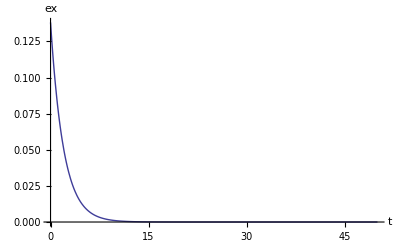

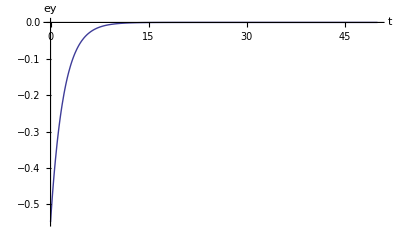

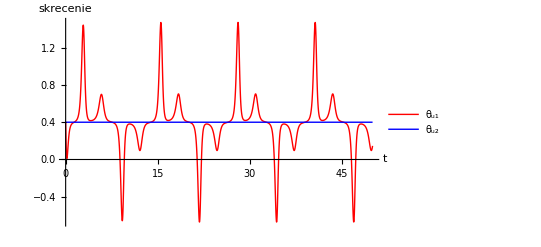

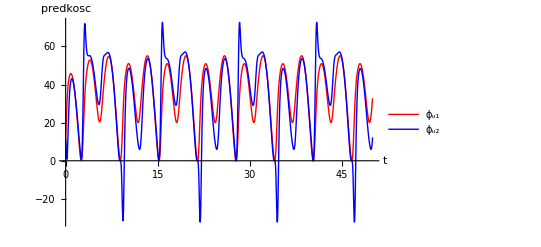

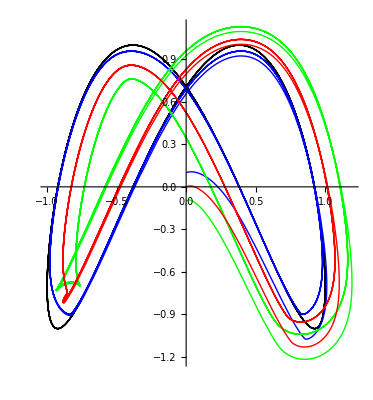

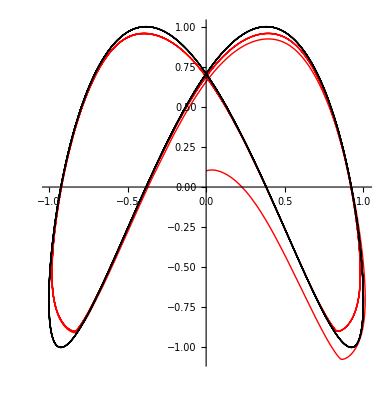

```mathematica
tmax = 50;
{xd[t_],yd[t_]}=osemka[t,1];
td[t_]=0.4;
d = 0.15;
h={x[t]+d*Cos[Subscript[θ, u1][t]+Subscript[θ, 0][t]],y[t]+d*Sin[Subscript[θ, u1][t]+Subscript[θ, 0][t]],Subscript[θ, u2][t]};(*Cos[Subscript[θ, u2][t]]+Cot[Subscript[θ, u1][t]]Sin[Subscript[θ, u2][t]]*)
hd={xd[t],yd[t],td[t]};
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, Subscript[θ, u1][0]==0.4, Subscript[ϕ, u1][0]==0, Subscript[θ, u2][0]== 0.4, Subscript[ϕ, u2][0]==0};
M =wyliczSterowanie[hd,h,0.5];
rozwiazanieu = rozwiazRownania[M,q0,tmax];
wyrysuj[rozwiazanieu,h,hd,tmax,True];
```

0

-0.15 r_1

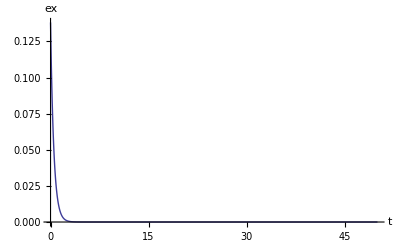

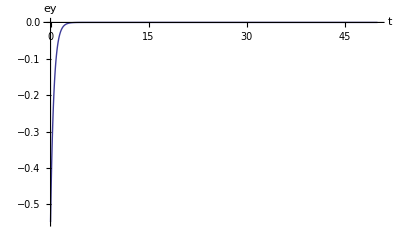

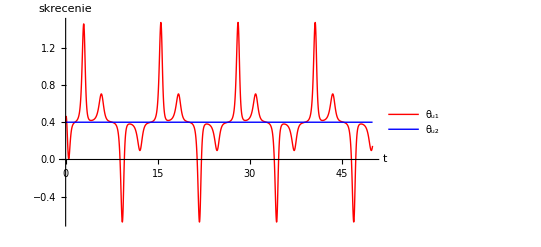

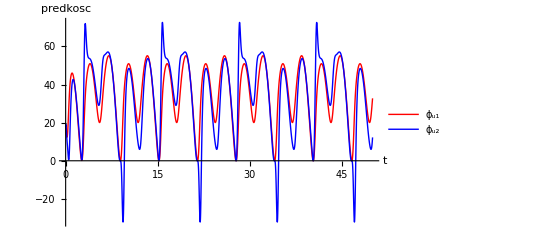

MapThread::mptd: Object None at position {2, 2} in MapThread[{EdgeForm[#1], #2} &, {{RGBColor[0.2472, 0.24, 0.6], RGBColor[0.6, 0.24, 0.442893], RGBColor[0.6, 0.547014, 0.24], RGBColor[0.24, 0.6, 0.33692]}, None}] has only 0 of required 1 dimensions.

MapThread::list: List expected at position 2 in MapThread[Directive[], Directive[RGBColor[0.24, 0.6, 0.33692]]].

MapThread::mptd: Object RGBColor[0.24, 0.6, 0.33692] at position {2, 1} in MapThread[{}, {RGBColor[0.24, 0.6, 0.33692]}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

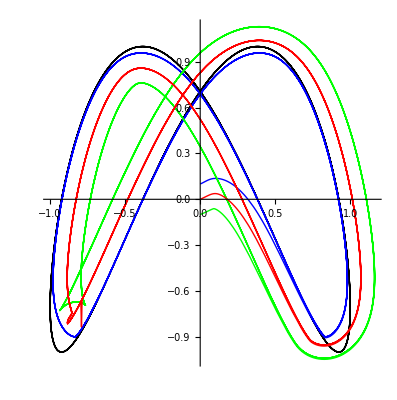

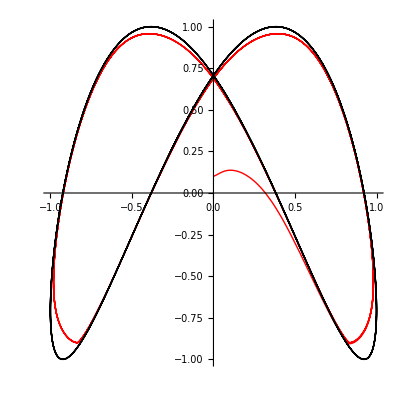

1

-0.15 r_1

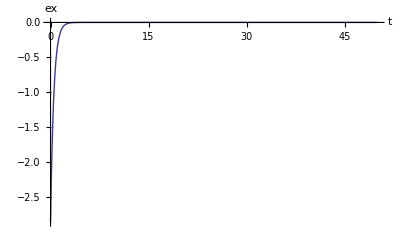

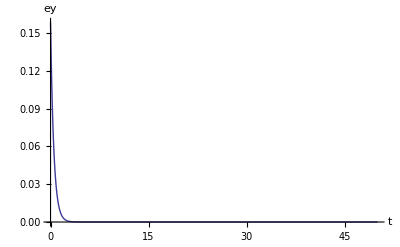

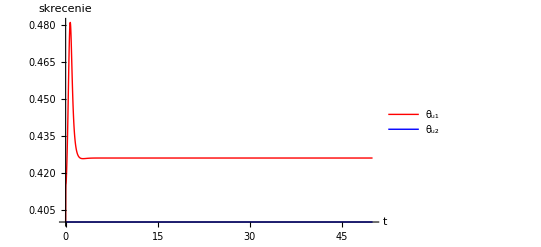

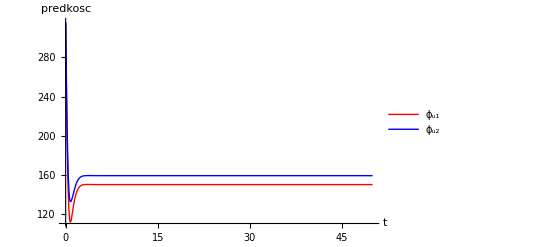

MapThread::list: List expected at position 2 in MapThread[Directive[], Directive[RGBColor[0.24, 0.6, 0.33692]]].

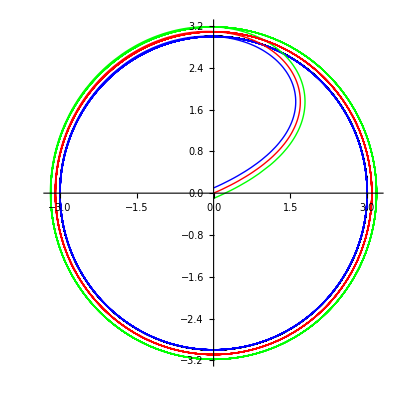

MapThread::list: List expected at position 2 in MapThread[Directive[], Directive[RGBColor[0.6, 0.24, 0.442893]]].

General::stop: Further output of MapThread :: list will be suppressed during this calculation.

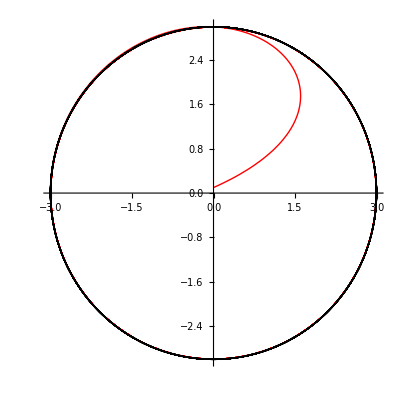

2

-0.15 r_1

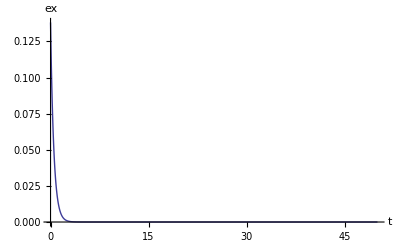

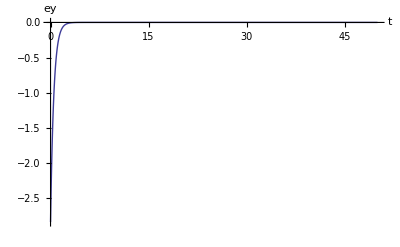

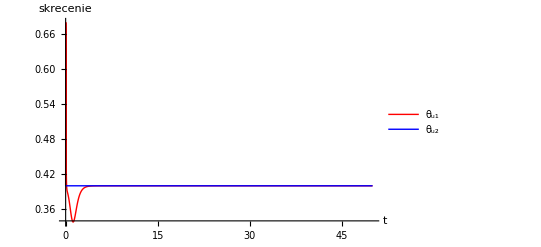

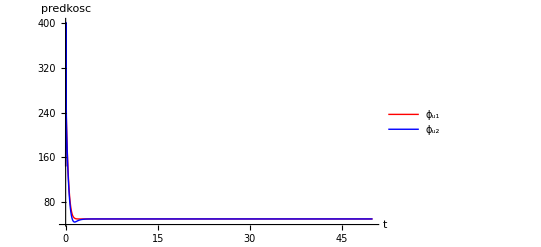

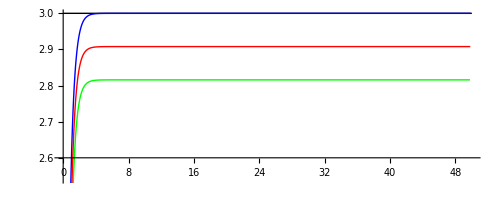

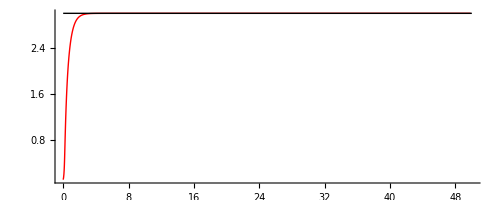

3

-0.15 r_1

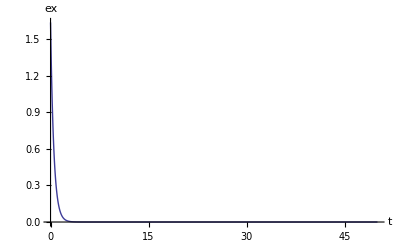

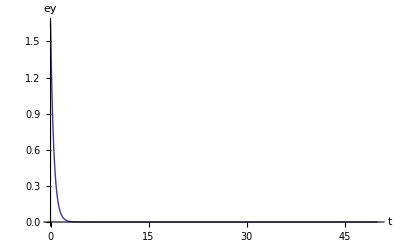

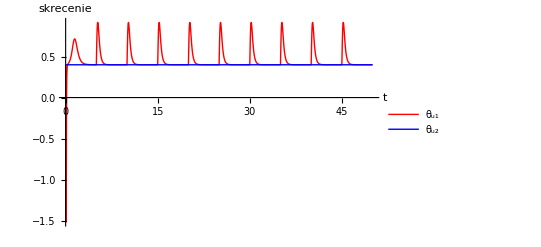

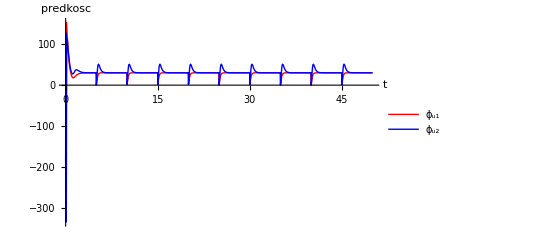

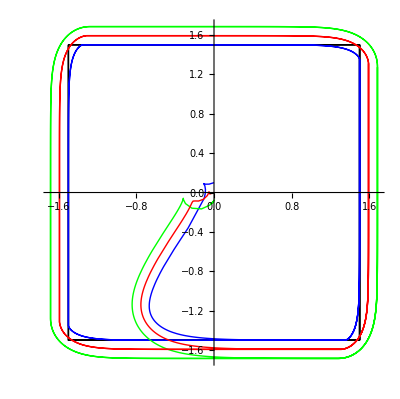

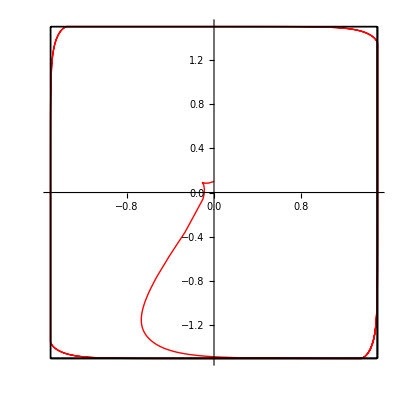

```mathematica
tmax = 50;
td[t_]=0.4;
d = 0.15;
w={x[t]+d*Cos[Subscript[θ, u1][t]+Subscript[θ, 0][t]],y[t]+d*Sin[Subscript[θ, u1][t]+Subscript[θ, 0][t]],Subscript[θ, u2][t]};(*Cos[Subscript[θ, u2][t]]+Cot[Subscript[θ, u1][t]]Sin[Subscript[θ, u2][t]]*)
q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0, Subscript[θ, u1][0]==0.4, Subscript[ϕ, u1][0]==0, Subscript[θ, u2][0]== 0.4, Subscript[ϕ, u2][0]==0};

For[i=0,i<4,i++,
Print[i];
Which[i==0,{xd[t_],yd[t_]}=osemka[t,1],i==1,{xd[t_],yd[t_]}=kolo[t,3,1],i==2,{xd[t_],yd[t_]}=liniaX[t,3,1],True,{xd[t_],yd[t_]}=kwadrat[t,3,5]];
wd={xd[t],yd[t],td[t]};
M = wyliczSterowanie[wd,w,2];
rozwiazanieu = rozwiazRownania[M,q0,tmax];
wyrysuj[rozwiazanieu, w, wd,tmax,False];
];
```